## Definitions

```mathematica
PM={IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[μ_]:=PM⟦μ+1⟧
X[μ_,ν_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧]
X[μ_,ν_,ρ_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧,PM⟦ρ+1⟧]
zero2=ConstantArray[0,{2,2}];zero4=ConstantArray[0,{4,4}];
Hermitize[H_]:=(H+ConjugateTranspose[H])/2
```

## Hamiltonian

### 2 TIs, one shifted by {0,π}

```mathematica
HTI[k_]:=(1+Cos[k[[1]]]+Cos[k[[2]]])X[3,0]+Sin[k[[1]]]X[1,1]+Sin[k[[2]]]X[1,2]
```

```mathematica
H2TI[k_]:=ArrayFlatten[{{HTI[k],zero4},{zero4,HTI[k+{0,Pi}]}}]
```

```mathematica
C2=KroneckerProduct[X[0,0],MatrixExp[I Pi/2 X[3]]];T=X[0,0,2];
```

### Symmetry allowed terms

```mathematica
(Position[Table[Norm[C2.X[i,j,k].Inverse[C2]-X[i,j,k]]+Norm[T.Conjugate[X[i,j,k]].Inverse[T]-X[i,j,k]],{i,0,3},{j,0,3},{k,0,3}],0]-1)
```

{{0,0,0},{0,1,0},{0,2,3},{0,3,0},{1,0,0},{1,1,0},{1,2,3},{1,3,0},{2,0,3},{2,1,3},{2,2,0},{2,3,3},{3,0,0},{3,1,0},{3,2,3},{3,3,0}}

```mathematica
(*these gap the Wilson loop: even terms X[2,1,3], X[2,2,0]; odd terms X[1,0,2], X[1,3,1]*)
```

```mathematica
HBulk[k_]:=N[H2TI[k]+0.5X[2,1,3]+0X[1,0,2]Sin[k[[2]]]]
dimH=Length[HBulk[{1.,1.}]];
filling=1/2;
```

```mathematica
Norm[C2.HBulk[{1.,2.}].Inverse[C2]-HBulk[-{1.,2.}]]+Norm[T.Conjugate[HBulk[{1.,2.}]].Inverse[T]-HBulk[-{1.,2.}]]+Norm[T.Conjugate[C2].Inverse[T]-C2]
```

4.44089×10^-16

```mathematica
(*ListPlot3D[Transpose[ParallelTable[Sort[Eigenvalues[HBulk[{kx,ky}]]],{kx,-Pi,Pi,0.1},{ky,-Pi,Pi,0.1}],{2,3,1}]]*)
```

## Wilson Loop

```mathematica
eigsysloc[{kx_,ky_}] := Block[{es=Eigensystem[HBulk[{kx,ky}]]},es⟦2,Ordering[Re[es⟦1⟧]]⟧][[1;;filling dimH]];
```

```mathematica
Proj[k_]:=Sum[Outer[Times,eigsysloc[k][[i]],Conjugate[eigsysloc[k][[i]]]],{i,filling dimH}]
```

### Wx

```mathematica
Wx[ky_]:=Conjugate[eigsysloc[{0,ky}]].(Dot@@Table[Proj[{k,ky}],{k,0,2Pi,2Pi/64}]).Transpose[eigsysloc[{2Pi,ky}]];
```

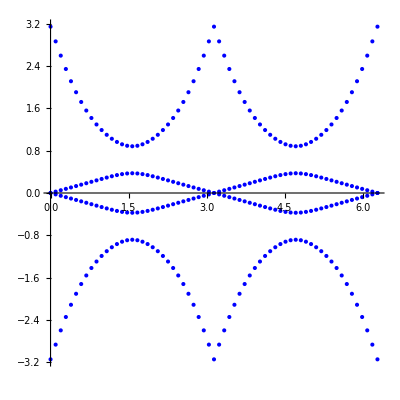

```mathematica
ListPlot[Transpose@ParallelTable[Im@Log@Eigenvalues[Wx[ky]],{ky,0,2Pi,2Pi/64}],PlotStyle->Blue,DataRange->{0,2Pi},PlotRange->{-Pi,Pi},GridLines->{{Pi},{-Pi,Pi}},AspectRatio->1]
```

### Wy of Wx

```mathematica
eigsysWx[ky_] := Block[{es=Eigensystem[Hermitize[-I MatrixLog[Wx[ky]]]]},(es⟦2,Ordering[Abs[es⟦1⟧]]⟧).eigsysloc[{2Pi,ky}]][[1;;2]];(*singling out the center Wilson band*)
```

```mathematica
ProjWx[ky_]:=Block[{esys=eigsysWx[ky]},Sum[Outer[Times,esys[[i]],Conjugate[esys[[i]]]],{i,2}]]
```

```mathematica
WyWx=Conjugate[eigsysWx[0]].(Dot@@Table[ProjWx[ky],{ky,0,2Pi,2Pi/64}]).Transpose[eigsysWx[2Pi]];
```

```mathematica
Im@Log@Eigenvalues[WyWx]/Pi
```

{1.,1.}